{{x→0},{x→2/3}}

{{x→0},{x→2/3},{x→2/3},{x→2/3}}

2/3

2/3

2/3

{0.05,0.11875,0.261621,0.482939,0.624272,0.586391,0.606341,0.596729,0.601609,0.599189,0.600404,0.599798,0.600101,0.599949,0.600025,0.599987,0.600006,0.599997,0.600002,0.599999,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6,0.6}

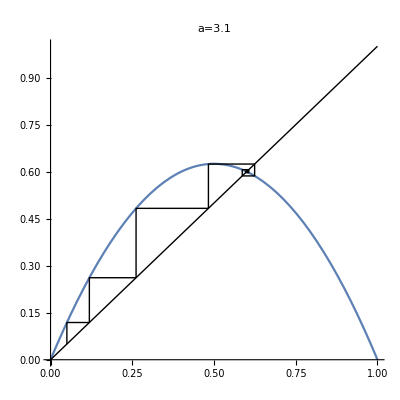

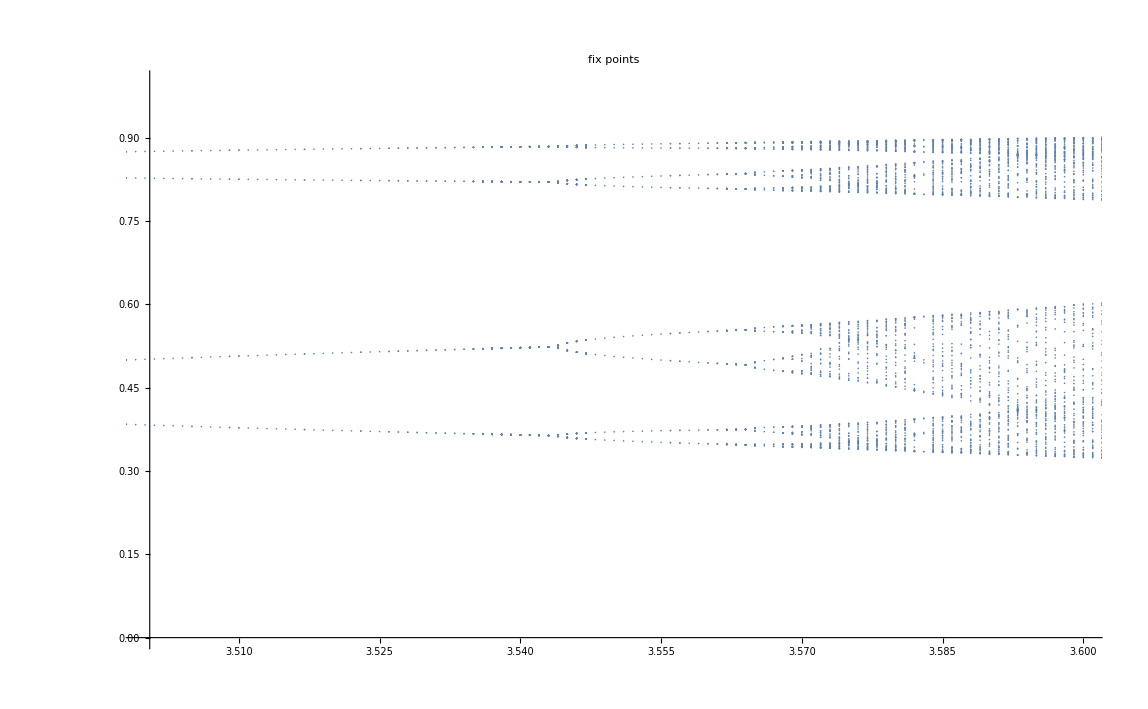

```mathematica
Clear["`*"]
(* This program solves the logistic map. It is a non-linear problem, note -x^2 on next line, and RSolve can not be used.
Instead Nest and NestList are used *)
a=3; (* another way to clear parameter a. 0<a<4. The really interesting region is between 3 and 4*)
g[x_]:=a x (1-x);
(* x_(n+1)=g(x_(n)), parameter a is in example below 3.1. x_0=0.5=start and we do 50 iterations in this example*)
solg1=Solve[x==g[x],x] //Simplify
solg2=Solve[x==g[g[x]],x] //Simplify
(* but first we find fix points of g with solg1. Especially the second element in the list is interesting. It is the only fix point
which is different from zero. It is created at a=1 when x=0 fix point becomes unstable. solg2 gives the period 2 solutions. That is
the fix points of g(g(x)). Here we are interested of the genuine period 2 solution which are the third and fourth elements in the list 
At http://en.wikipedia.org/wiki/Logistic_map you can read about this map. There you see that the period 2 solution was created at a=3
when the fix point to the right became unstable.*) 
a=2.5; start=0.05;iter=30;
xfp= x /. solg1[[2]]
x2c1=x /. solg2[[3]]
x2c2=x /. solg2[[4]]
(* Last lines give numerical values for fix point and period 2 solution *)
(* The following lines you don't have think about. It produces an illuminating plot
of the iterations *)
points=NestList[g,start,iter-1]
lines[x_]:=Line[{{x,x},{x,g[x]},{g[x],g[x]}}]
listlines=lines/@ points;
Plot[ g[x],{x,0,1},
AspectRatio->Automatic,
PlotLabel->"a=3.1",
PlotRange->{{0,1},{0,1}},
Epilog->{Line[{{0,0},{1,1}}],listlines}]
(* Below follows commands that generate the bifurcation diagram in the interesting region 3<a<4.  *)
nstart=500;number=128;
(* It works like this I think: after 500 iterations the program takes a look at the following 128
iterations. Union takes away doublets etc. Left is the stable periodic orbit. In the region from
a=3.6 to 4 there is a lot of chaos, that is no stable periodic orbit at all. But in some places
there is a "window". A sign of a short stable periodic orbit *)
afixpoint:=
Union[
Map[
{a,#}&,
NestList[g,Nest[g,start,nstart],number-1]
]
];
amin=3.;amax=3.999;step=0.001;
fixpoints=Flatten[Table[afixpoint,{a,amin,amax,step}],1];
ListPlot[ fixpoints,
PlotLabel->"fix points",
PlotRange->{{3.5,3.6},{0,1}},
PlotStyle->PointSize[0.001]]
```